# CryptoRave 2017 Criptografia com Automatos Celulares

## Daniel Carvalho @danielscarvalho Advisor Tecnologia

## Cryptografia com CA

### CryptoRave 2017

Os autômatos celulares (AC) foram estudados por Alan Turing, John Von Neumann, John Conway e mais recentemente por Stephen Wolfram. Este modelo computacional simples tem diversas aplicações inclusive em criptografia e geração de números aleatórios. Regras computacionais simples podem gerar resultados complexos (sofisticados).

Será realizada uma apresentação bastante visual e interativa sobre criptografia, um panorama geral, os cientistitas que estudaram AC, demonstração sobre autômatos celulares, geração de números aleatórios com AC, “Game of Life”, “glider” e o logo hacker, como criptografar dados com AC e como esconder informação em imagens por exemplo.

Dia: 05/05/2017 
Hora de início: 23:50 
Duração: 00:50 
Room: Edward Snowden 
Trilha: Criptografia 
Language: en

Casa do Povo - Rua Três Rios, 252 - Bom Retiro - São Paulo

Cryptorave

Programação

-Graphics-

## Breve História

### John von Neumann

1903-1957 (53) a 113 anos - Budapest, Hungary

-Graphics-

Hungarian-American mathematician,considered one of the greatest mathematicians in history for his many contributions to numerous mathematical fields

Contributed to the development of the hydrogen bomb and was a key member of the Manhattan Project

Principal figure in the development of such concepts as game theory,cellular automata,the universal constructor,and the digital computer

John von Neumann

## Breve História

### Alan Turing

1912-1954 (41) a 104 anos - London, United Kingdom

-Graphics-

Mathematician known for his pioneering work in the fields of computer science, artificial intelligence, and cryptanalysis

Created techniques to break German ciphers for Great Britain during World War II, including the famous Enigma Machine

Developed the "Turing test" to define a standard by which a computer or program could be considered "intelligent"

Formulated the halting problem and then proved it undecidable in 1936
Prosecuted in Great Britain for homosexuality and died shortly thereafter, likely by suicide

Alan Turing

## Breve História

### John Conway - Game of Life

1937 (79) - Liverpool, United Kingdom

-Graphics-

John Horton Conway FRS (born 26 December 1937) is an English mathematician active in the theory of finite groups, knot theory, number theory, combinatorial game theory and coding theory. He has also contributed to many branches of recreational mathematics, notably the invention of the cellular automaton called the Game of Life. Conway is currently Professor Emeritus of Mathematics at Princeton University in New Jersey.

John Conway

## Breve História

### Stephen Wolfram

1959 (57) - London, United Kingdom

-Graphics-

Founder and CEO of Wolfram Research
Creator of Mathematica, Wolfram|Alpha, and the Wolfram Language
Author of A New Kind of Science
Pioneer in studying cellular automata
Contributed to founding the field of complexity theory

Stephen Wolfram

## Breve História

### New Kind of Science - Stephen Wolfram

-Graphics-

https://www.wolframscience.com/

New Kind of Science

## Criptografia

Criptografia fraca:

-Graphics-

Criptografia de verdade:

-Graphics-
Enigma

U-571: A Batalha do Atlântico

Quebrando a criptografia sofisticada:

-Graphics-
How Designers Recreated Alan Turing’s Code-Breaking Computer for Imitation Game

Criptografia é fácil de ser utilizada por usuários ou programadores, porém não é popular.

Criar algoritmos de criptografia é complexo, requer uso de matemática sofisticada, e é difícil de validar um novo algoritmo.

-Graphics-

-Graphics-

Tipos básicos:

- Simétrica, chave única (remetente e destinatário usam a mesma senha)
- Assimétirca, chave pública e privada (GPG, RSA)

## Automatos Celulares

Modelo computacional com base em regras simples.
E capaz de realizar computação universal.
Sistema Dinâmico Discreto.

```mathematica
Manipulate[
Grid[{
{Text@"decimal rule expanded in powers of 2",SpanFromLeft},{} ,
{Text@Style[Row@Append[Append[Drop[Flatten[Riffle[IntegerDigits[rule,2,8],Table[{" × ",2^x2, "  +  "},{x2,7,0,-1}]]],-1]," == "],rule],ColorData["HTML","Green"], Bold],SpanFromLeft},{} ,
{Text@"binary representation of rule",SpanFromLeft},{},
 Text@Row[Style[#,ColorData["HTML","SlateBlue"],Bold]&/@IntegerDigits[#,2,3],"   "]&/@Table[x,{x,7,0,-1}],
Style[#,ColorData["HTML","SlateBlue"],Bold]&/@ IntegerDigits[rule,2,8],{},
{Text@"graphic representation of rule",SpanFromLeft},{},
ArrayPlot[{#},ImageSize-> 50,Mesh-> True,ColorRules-> {0-> White, 1-> Black}] &/@ Tuples[{1,0},3],
ArrayPlot[{#},ImageSize-> 15,Mesh-> True,ColorRules-> {0-> White, 1-> Black}] &/@ Partition[IntegerDigits[rule,2,8],1],
{ArrayPlot[CellularAutomaton[rule,{{1},0},{steps,All}],ImageSize-> {350,200},Mesh-> mesh,ColorRules-> {0-> White, 1-> Black}],SpanFromLeft}},Alignment-> Center,Frame-> None,Spacings->{.5,0}],
{{rule,110,"rule as decimal"},0,255,1,Appearance-> "Labeled"},
{steps,10,50,1},
{mesh,{True,False}}]
```

```mathematica
Manipulate[ArrayPlot[
CellularAutomaton[rule,{{1},0},steps],
PlotLabel-> rule, 
ColorRules-> {0-> White,1-> Black},
Frame-> None,
Mesh->mesh],
{rule,0,255,1},
{{steps,100},0,100,1},
{{rule,90},{45,30,90,110, 135}},
{mesh,{None,True}}]
```

```mathematica
Manipulate[ArrayPlot[
CellularAutomaton[rule,RandomInteger[1,100],100], 
ColorRules-> {0-> White,1-> Black},
Frame-> None,
PlotLabel-> rule],
{rule,0,255,1}]
```

## Imprevisibilidade (Unpredictability) e Irreversibilidade (Irreversibility) Computacional

Para saber o comportamento da etapa (step, time) 10.000 é necessário calcular todos os passos anteriores. A saída de uma etapa é a entrada da próxima (sistema dinâmico).

Custo computacional elevado para calcular o passo anterior.

```mathematica
ArrayPlot[CellularAutomaton[30,RandomInteger[1,40],40], Frame-> None, PixelConstrained->14, ColorRules-> {0-> White, 1-> Black}]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[30,RandomInteger[1,400],400], Frame-> None, PixelConstrained->2, ColorRules-> {0-> White, 1-> Black}]
```

-Graphics-

## Usando CA para gerar hash code

Apenas pesquisa!! Não é confiável! Use algoritmos consolidados!!

Usar texto de entrada como condição inicial para o CA: “Hellow World”

```mathematica
hw=ToCharacterCode["Hellow World"]
```

{72,101,108,108,111,119,32,87,111,114,108,100}

```mathematica
IntegerDigits[#,2,8]&/@ hw
init=Flatten[%]
```

{{0,1,0,0,1,0,0,0},{0,1,1,0,0,1,0,1},{0,1,1,0,1,1,0,0},{0,1,1,0,1,1,0,0},{0,1,1,0,1,1,1,1},{0,1,1,1,0,1,1,1},{0,0,1,0,0,0,0,0},{0,1,0,1,0,1,1,1},{0,1,1,0,1,1,1,1},{0,1,1,1,0,0,1,0},{0,1,1,0,1,1,0,0},{0,1,1,0,0,1,0,0}}

{0,1,0,0,1,0,0,0,0,1,1,0,0,1,0,1,0,1,1,0,1,1,0,0,0,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,0,0,1,0,0,0,0,0,0,1,0,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,0,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0,0,1,0,0}

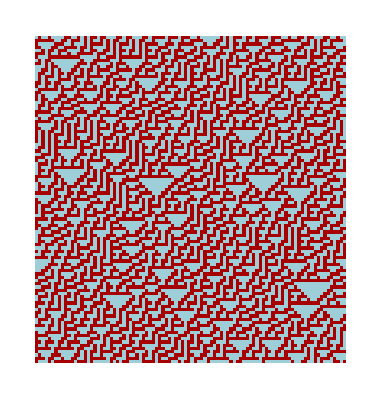

```mathematica
ArrayPlot[caEncoded=CellularAutomaton[30,init,100]]
```

```mathematica
Last[caEncoded]
```

```mathematica
{1,0,0,0,1,0,1,1,1,1,1,1,0,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,1,1,0,1,1,1,1,0,0,1,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1}
```

```mathematica
FromDigits[#,2]&/@Partition[Last[caEncoded],8]
Text[FromCharacterCode[%]]
```

{139,247,65,88,123,203,68,11,2,1,50,141}

.8b÷AX{ËD.0b.02.01.012.8d

```mathematica
CAEncode[message_]:= Module[{caInit=Flatten[IntegerDigits[#,2,8]&/@ToCharacterCode[message]]},
FromCharacterCode[FromDigits[#,2]&/@Partition[CellularAutomaton[30,caInit,{{1000}}]⟦1⟧,8]]];
```

```mathematica
CAEncode["Vai Corinthians!!"]
```

.9cèÈ.91NÇñJq¶@.0féë9n.1f

```mathematica
CAEncode["CryptoRave 2017"]
```

|.83Ë\&Æ'Ñ.1ak.841.18xÐ

Hash function

```mathematica
IntegerString[Hash["Vai Corinthians","MD5"],16,32]
```

c3fc38158b6890103e9029a2535a6096

```mathematica
IntegerString[Hash["Vai Corinthians","SHA512"],16,32]
```

f567dcd5885d5f20c80425bfc46cc9ec

Arquivo de senhas no UNIX/Linux: /etc/shadow

smithj:Ep6mckrOLChF.:10063:0:99999:7:::
root:9v0SF$hjztYvo:16431:0:99999:7:::
mandar:$6$5H0QpwprRi:16431:0:99999:7:::
mysql:!!:16550::::::
nagios:$6$P9zn0tgfvv:16632:0:99999:7:::

Salt: Proteção contra ataques de dicionários
One way function: Função irreversível
MongoDB, CouchDB (NoSQL Document DB): Utilizam hash code para cada documento da base

Vernam cipher key generator:

texto original + chave = texto cifrado ⇒ texto cifrado + chave = texto original (decifrado)

+ → XOR  ⊗

-Graphics-

Combinando multiplas chaves simétricas, ou multiplas regras de CA:

-Graphics-

-Graphics-

## CA Regra 30 Aleatoriedade

A as células centrais da regra 30 tem comportamento aleatório, pode ser utilizado para geração de números pseudo aleatórios.

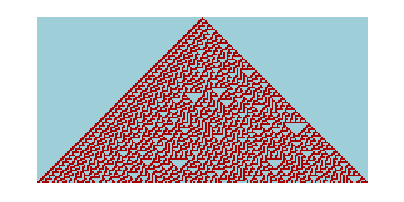

```mathematica
ArrayPlot[ca30=CellularAutomaton[30,{{1},0},99]]
```

```mathematica
ca30rand=ca⟦All,Length[ca30]/2⟧
```

{0,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1}

```mathematica
SeedRandom[Method->"Rule30CA"]
Manipulate[ListLinePlot[RandomInteger[100,step]],{step,10,500,1}]
```

```mathematica
Manipulate[
SeedRandom[sr];
Grid[{{TraditionalForm@constant,Text@"random number"},
{ArrayPlot[Partition[constList=RealDigits[N[constant,size^2]]⟦1⟧,size],ColorRules->{digit->Red},Frame-> False, ImageSize-> {275,275}],
ArrayPlot[Partition[randList=RandomInteger[9,size^2],size],ColorRules->{digit->Red},Frame-> False, ImageSize-> {275,275}]},
{Text@Row[{"mean: ",N@Mean[constList]}],Text@Row[{"mean: ",N@Mean[randList]}]},
{Text@Row[{"total: ",N@Total[constList]}],Text@Row[{"total: ",N@Total[randList]}]}
},Frame-> All],
{{size,3},1,100,1},
{{digit,1},0,9,1},
{{constant,Pi},{Pi-> TraditionalForm@Pi,GoldenRatio-> TraditionalForm@GoldenRatio,E -> TraditionalForm@E,EulerGamma-> TraditionalForm@EulerGamma}},
{{sr,1234,"random seed"},1,12345,1},TrackedSymbols->Manipulate]
```

Como gerar números aleatórios??
Hardware, ruído branco...

## Cellular Automata Explorer

From Wolfram Demonstration Project

Maior vizinhança
Mais cores
Totalistico
Etc

```mathematica
Manipulate[Catch[Quiet[(If[Head[#]=!=Graphics,Throw[Pane[Framed[Text[Style["rule number out of range",14,Italic]],Background->LightYellow],{600,300},Alignment->Center]],#]&@ArrayPlot[CellularAutomaton[{Round[rn],If[OddQ[rt],k,{k,1}],r},ic/.{1->{{1},0},2->{{1,1},0},3->(SeedRandom[23424];RandomInteger[k-1,2r t])},{t,All}],PlotLabel->Style[Row[{If[OddQ[rt],"rule ","totalistic code "],Round[rn]}],11,"Label"],ImageSize->600,ColorRules->cmap,Mesh->mesh])//If[rd==1,#,Column[{#,With[{f=ArrayPlot[{#},Mesh->True,ColorRules->cmap,ImageSize->{Automatic,10},AspectRatio->1/#2]&,bits=IntegerDigits[Round[rn],k,If[OddQ[rt],k^(2 r+1),(1+(k-1)(2r+1))]]},
Switch[rd,1,SpanFromAbove,2,Row[f[{#},1]&/@bits],3,GraphicsRow[MapThread[GraphicsColumn[{f[#,2r+1],f[{#2},1]},Center,Spacings->0]&,{If[OddQ[rt],Tuples[Reverse[Range[0,k-1]],2 r+1],List/@If[cmap===Automatic,#&,Blend[Range[0,k-1]/.cmap,#]&]/@Reverse[(Range[0,#]/#)&[(k-1)(2r+1)]]],bits}],Spacings->0,Frame->All]]]},Center]]&]],{{k,2,"colors"},{2,3,4,5}},
{{r,1,"range"},{1/2->"1/2",1->1,3/2->"3/2",2->2}},
{{rt,1,"rule type"},{1->"general",2->"totalistic",3->"general (quiescent)",4->"totalistic (quiescent)"}},{{ic,1,"initial condition"},{1->"single cell",2->"two cells",3->"random"}},
 Delimiter,
{{rn,If[rt==1&&k==2&&r==1,150,0],"rule number"},0,If[OddQ[rt],Min[k^(k^(2 r+1))-1,2000],k^(1+(k-1) (2 r+1))-1],If[rt>2,k,1]},
Delimiter,
{{t,50,"steps"},0,200,1},{{cmap,Automatic,"color map"},{Automatic->"gray scale",{0->White,1->Red,2->Blue,3->Green,4->Yellow}->"primary colors",{0->White,1->Pink,2->Purple,3->Yellow,4->Orange}->"pastels"}},{{mesh,False,"show mesh"},{True,False}},{{rd,1,"rule display"},{1->"none",2->"bits",3->"icon"}}, ControlPlacement->Top,AutorunSequencing->{1,2,3,4,6,7,8,9}]
```

## CA e padrões naturaes

É possível buscar regras de CA que representam padrões encontrados na natureza

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Turing Bio Patterns
NKS

## Quatro classes de comportamento

Classe I - Converge para branco (0) ou preto (1)
Classe II - Padrão Repetitivo
Classe III - Aleatório
Classe IV - Aleatório e Repetitivo (Complexo)

```mathematica
Manipulate[ArrayPlot[
CellularAutomaton[rule,RandomInteger[1,100],100]],
{rule,0,100,1}]
```

```mathematica
Manipulate[Row[{
ArrayPlot[ca=CellularAutomaton[rule,RandomInteger[1,100],100],ImageSize-> 300],
ListLinePlot[catotal=Total[Transpose[ca]],ImageSize-> 300],
Histogram[catotal,ImageSize-> 300]
}],
{rule,0,255,1}]
```

```mathematica
compressedCARules=Reverse[Sort[Table[{ByteCount[Compress[#]],carule,#}&[CellularAutomaton[carule,RandomInteger[1,70],70]],{carule,0,255,1}]]];
byteList=compressedCARules[[All,1]];
Manipulate[
ListLinePlot[byteList,PlotStyle-> Thick,Filling->Axis,AxesLabel->{"rules","bytes"},ColorFunction->"Rainbow",
Epilog->{Thick,Black,Line[{{rule,2000},{rule,0}}],Inset[ArrayPlot[compressedCARules⟦rule,3⟧,PixelConstrained -> 2],{210,1250}]},ImageSize-> {450,300},PlotLabel-> Text[Style[Grid[{{"rule",compressedCARules⟦rule,2⟧},{"bytes",compressedCARules⟦rule,1⟧}},Alignment-> Right]
,Black]],AxesOrigin->{1,0}],
{{rule,50},1,256,1},ContinuousAction->False,TrackedSymbols-> Manipulate, SaveDefinitions-> True]
```

## CA Elementares

256 regras = 2^8

Duas cores
3 vizinhos
Condição inicial aleatória

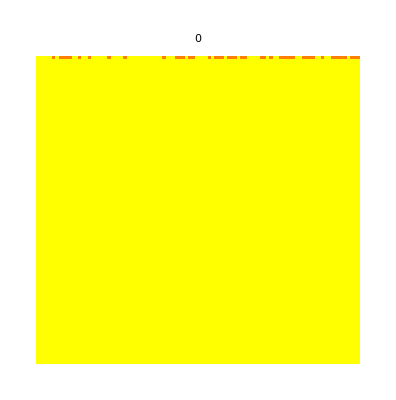
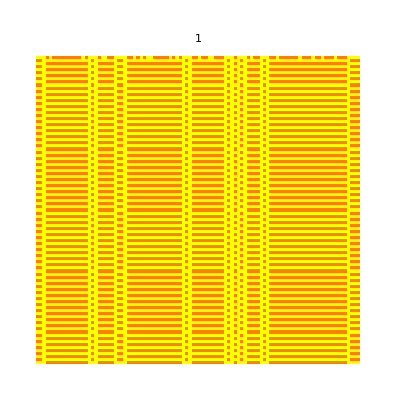
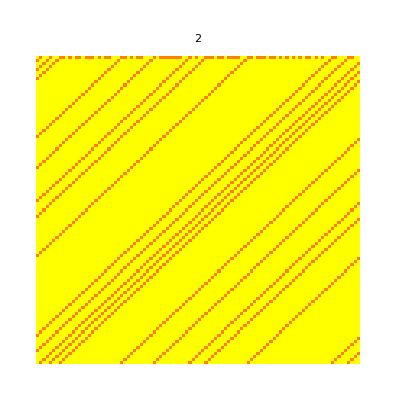
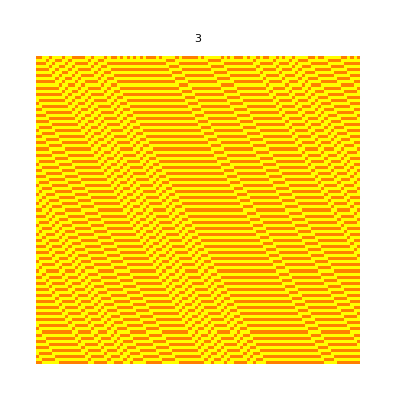
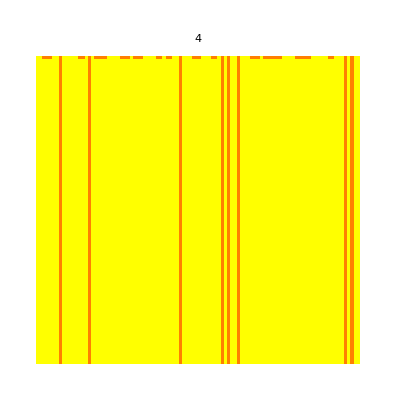
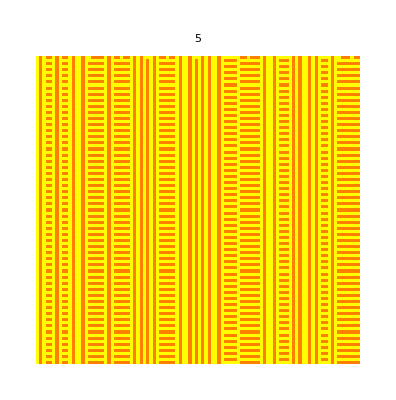
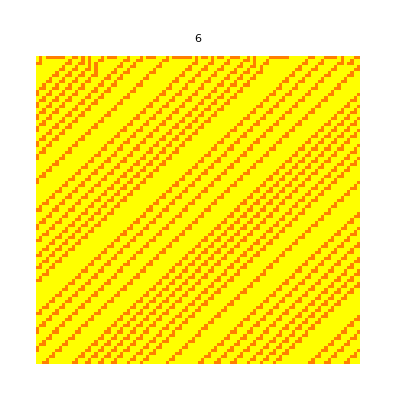
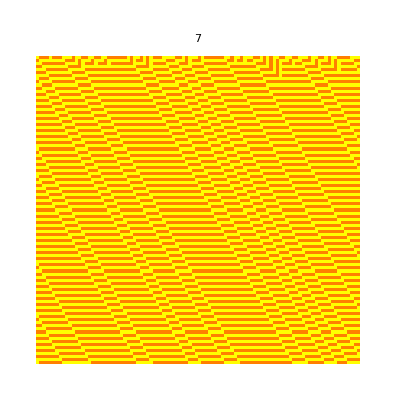
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[Table[ArrayPlot[CellularAutomaton[rule, RandomInteger[1,100],100],Frame-> None,PlotLabel-> rule, ColorRules-> {0-> Yellow, 1-> Orange}],{rule, 0, 255, 1}],4]]
```

## Jogo da Vida

CA 2D: Regra

1. Células vivas com menos de dois vizinhos vivos morre de solidão.
2. Células vivas com mais de três vizinhos vivos morre de superpopulação.
3. Células mortas com exatamente três vizinhos vivos se torna uma célula viva.
4. Células vivas com dois ou três vizinhos vivos continua no mesmo estado para a próxima geração.

-Graphics-
Fonte: NKS, Life in a shade of ruby

Vizinhança (Moore neighborhood):

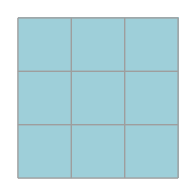

```mathematica
ArrayPlot[{{0,0,0},{0,0,0},{0,0,0}},Mesh-> True]
```

```mathematica
Manipulate[
Refresh[
If[oldlen≠len||oldp≠p,
oldlen=len;oldp=p;updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0
];
If[updating||onestep,
t++;
onestep=False;
config = Last[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},If[bg,{config,0},config],{{0,1}}]];
If[config=={},config={{0}}]
];
EventHandler[Dynamic[ArrayPlot[Reverse@config,PlotLabel->Row[{Style["t",Italic]," = "<>ToString[t]}],ImageSize->{400,400},AspectRatio->Automatic]],"MouseClicked":>(If[1<#[[1]]<Length[config]&&1<#[[2]]<Length[First[config]],config[[#[[2]],#[[1]]]]=1-config[[#[[2]],#[[1]]]]]&)[Ceiling@MousePosition["Graphics"]]]

,UpdateInterval->If[updating,0,Infinity]
]
,
{{updating,False,"run simulation"},{True,False}},
Button["update one step",onestep=True,ImageSize->Medium],
Button["reset",updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0,ImageSize->Small],
{{bg,False,"infinite space"},{True,False}},
{{len,50,"edge length"},30,200,10,Appearance->"Labeled",ImageSize->Tiny},
{{oldlen,50},ControlType->None},
{{p,0.1,"initial density"},0,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{oldp,0.1},ControlType->None},
{{t,0},ControlType->None},
{{config,Table[If[RandomReal[]<p,1,0],{50},{50}]},ControlType->None},
{{onestep,False},ControlType->None},
ControlPlacement->Left,
TrackedSymbols:>{updating,onestep,config,len,t,bg,p},AutorunSequencing->{3,5},SynchronousUpdating->True
]
```

```mathematica
arrayPlot[initialCondition_,mesh_,color_]:=ArrayPlot[initialCondition,Mesh-> mesh,ColorRules-> If[color,{1-> Orange, 0-> Yellow},{1-> Black,0-> White}],ImageSize-> 350,Frame-> False];
hackerPlot[initialCondition_,mesh_,color_] := GraphicsGrid[Map[If[#==1,Graphics[{If[color,Orange,Black],Disk[]}],""]&,initialCondition,{2}],Frame-> mesh,FrameStyle->Gray,Spacings->2,Background->If[color,Yellow,White] ];

Manipulate[
Pane[view[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},
SparseArray[If[matrixSize>3,Append[#,{matrixSize,matrixSize}-> 0],#]&[{{1,2}-> 1,{2,3}-> 1,{3,1}-> 1,{3,2}-> 1,{3,3}-> 1}]],
{{{step}}}],mesh,color],{350,350}],
{{matrixSize,10,"matrix size"},3,15,1},
{step,0,100,1},
{{view,hackerPlot},{hackerPlot-> "hacker",arrayPlot-> "traditional"}},
{{mesh,All},{All-> "yes",None-> "no"}},
{color,{False,True},ControlType-> Checkbox},SaveDefinitions->True,AutorunSequencing->{1,2,3,5}]
```

```mathematica
initialCondition={
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
}; (* turbine *)
Manipulate[
ArrayPlot[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},initialCondition,{{{step}}}],Mesh-> mesh,ColorRules-> If[color,{1-> Orange, 0-> Yellow},{1-> Black,0-> White}],ImageSize-> 400],
{step,0,16,1,Appearance->"Labeled"},
{mesh,{None,All},ControlType-> Checkbox},
{color,{True,False},ControlType-> Checkbox}, SaveDefinitions-> True]
```

Programa simulador de CA: Golly